```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
style1={FontFamily->"Helvetica",16,GrayLevel[0]};
ResourceFunction["AddMatplotlibColors"][]
NormalizedLaplacianMat[graph_]:=DiagonalMatrix[1/Sqrt[Diagonal[N[Normal[KirchhoffMatrix[graph]]]]]/.ComplexInfinity->0].N[Normal[KirchhoffMatrix[graph]]].DiagonalMatrix[1/Sqrt[Diagonal[N[Normal[KirchhoffMatrix[graph]]]]]/.ComplexInfinity->0]
```

{Magma,Inferno,Plasma,Viridis,EricsRdBuGnYl,EricsRdBuGnYl2,EricsPuBuGnYl,FakeParula,JoesBluGrnPnk2}

### i. add cividis colormap

```mathematica
cividis=Module[{colorlist},colorlist={{0,0.1321,0.3142},{0,0.135,0.3205},{0,0.1379,0.3269},{0,0.1408,0.3334},{0,0.1437,0.34},{0,0.1465,0.3467},{0,0.1492,0.3537},{0,0.1519,0.3606},{0,0.1546,0.3676},{0,0.1574,0.3746},{0,0.1601,0.3817},{0,0.1629,0.3888},{0,0.1657,0.396},{0,0.1685,0.4031},{0,0.1714,0.4102},{0,0.1743,0.4172},{0,0.1773,0.4241},{0,0.1798,0.4307},{0,0.1817,0.4347},{0,0.1834,0.4363},{0,0.1852,0.4368},{0,0.1872,0.4368},{0,0.1901,0.4365},{0,0.193,0.4361},{0,0.1958,0.4356},{0,0.1987,0.4349},{0,0.2015,0.4343},{0,0.2044,0.4336},{0,0.2073,0.4329},{0.0055,0.2101,0.4322},{0.0236,0.213,0.4314},{0.0416,0.2158,0.4308},{0.0576,0.2187,0.4301},{0.071,0.2215,0.4293},{0.0827,0.2244,0.4287},{0.0932,0.2272,0.428},{0.103,0.23,0.4274},{0.112,0.2329,0.4268},{0.1204,0.2357,0.4262},{0.1283,0.2385,0.4256},{0.1359,0.2414,0.4251},{0.1431,0.2442,0.4245},{0.15,0.247,0.4241},{0.1566,0.2498,0.4236},{0.163,0.2526,0.4232},{0.1692,0.2555,0.4228},{0.1752,0.2583,0.4224},{0.1811,0.2611,0.422},{0.1868,0.2639,0.4217},{0.1923,0.2667,0.4214},{0.1977,0.2695,0.4212},{0.203,0.2723,0.4209},{0.2082,0.2751,0.4207},{0.2133,0.278,0.4205},{0.2183,0.2808,0.4204},{0.2232,0.2836,0.4203},{0.2281,0.2864,0.4202},{0.2328,0.2892,0.4201},{0.2375,0.292,0.42},{0.2421,0.2948,0.42},{0.2466,0.2976,0.42},{0.2511,0.3004,0.4201},{0.2556,0.3032,0.4201},{0.2599,0.306,0.4202},{0.2643,0.3088,0.4203},{0.2686,0.3116,0.4205},{0.2728,0.3144,0.4206},{0.277,0.3172,0.4208},{0.2811,0.32,0.421},{0.2853,0.3228,0.4212},{0.2894,0.3256,0.4215},{0.2934,0.3284,0.4218},{0.2974,0.3312,0.4221},{0.3014,0.334,0.4224},{0.3054,0.3368,0.4227},{0.3093,0.3396,0.4231},{0.3132,0.3424,0.4236},{0.317,0.3453,0.424},{0.3209,0.3481,0.4244},{0.3247,0.3509,0.4249},{0.3285,0.3537,0.4254},{0.3323,0.3565,0.4259},{0.3361,0.3593,0.4264},{0.3398,0.3622,0.427},{0.3435,0.365,0.4276},{0.3472,0.3678,0.4282},{0.3509,0.3706,0.4288},{0.3546,0.3734,0.4294},{0.3582,0.3763,0.4302},{0.3619,0.3791,0.4308},{0.3655,0.3819,0.4316},{0.3691,0.3848,0.4322},{0.3727,0.3876,0.4331},{0.3763,0.3904,0.4338},{0.3798,0.3933,0.4346},{0.3834,0.3961,0.4355},{0.3869,0.399,0.4364},{0.3905,0.4018,0.4372},{0.394,0.4047,0.4381},{0.3975,0.4075,0.439},{0.401,0.4104,0.44},{0.4045,0.4132,0.4409},{0.408,0.4161,0.4419},{0.4114,0.4189,0.443},{0.4149,0.4218,0.444},{0.4183,0.4247,0.445},{0.4218,0.4275,0.4462},{0.4252,0.4304,0.4473},{0.4286,0.4333,0.4485},{0.432,0.4362,0.4496},{0.4354,0.439,0.4508},{0.4388,0.4419,0.4521},{0.4422,0.4448,0.4534},{0.4456,0.4477,0.4547},{0.4489,0.4506,0.4561},{0.4523,0.4535,0.4575},{0.4556,0.4564,0.4589},{0.4589,0.4593,0.4604},{0.4622,0.4622,0.462},{0.4656,0.4651,0.4635},{0.4689,0.468,0.465},{0.4722,0.4709,0.4665},{0.4756,0.4738,0.4679},{0.479,0.4767,0.4691},{0.4825,0.4797,0.4701},{0.4861,0.4826,0.4707},{0.4897,0.4856,0.4714},{0.4934,0.4886,0.4719},{0.4971,0.4915,0.4723},{0.5008,0.4945,0.4727},{0.5045,0.4975,0.473},{0.5083,0.5005,0.4732},{0.5121,0.5035,0.4734},{0.5158,0.5065,0.4736},{0.5196,0.5095,0.4737},{0.5234,0.5125,0.4738},{0.5272,0.5155,0.4739},{0.531,0.5186,0.4739},{0.5349,0.5216,0.4738},{0.5387,0.5246,0.4739},{0.5425,0.5277,0.4738},{0.5464,0.5307,0.4736},{0.5502,0.5338,0.4735},{0.5541,0.5368,0.4733},{0.5579,0.5399,0.4732},{0.5618,0.543,0.4729},{0.5657,0.5461,0.4727},{0.5696,0.5491,0.4723},{0.5735,0.5522,0.472},{0.5774,0.5553,0.4717},{0.5813,0.5584,0.4714},{0.5852,0.5615,0.4709},{0.5892,0.5646,0.4705},{0.5931,0.5678,0.4701},{0.597,0.5709,0.4696},{0.601,0.574,0.4691},{0.605,0.5772,0.4685},{0.6089,0.5803,0.468},{0.6129,0.5835,0.4673},{0.6168,0.5866,0.4668},{0.6208,0.5898,0.4662},{0.6248,0.5929,0.4655},{0.6288,0.5961,0.4649},{0.6328,0.5993,0.4641},{0.6368,0.6025,0.4632},{0.6408,0.6057,0.4625},{0.6449,0.6089,0.4617},{0.6489,0.6121,0.4609},{0.6529,0.6153,0.46},{0.657,0.6185,0.4591},{0.661,0.6217,0.4583},{0.6651,0.625,0.4573},{0.6691,0.6282,0.4562},{0.6732,0.6315,0.4553},{0.6773,0.6347,0.4543},{0.6813,0.638,0.4532},{0.6854,0.6412,0.4521},{0.6895,0.6445,0.4511},{0.6936,0.6478,0.4499},{0.6977,0.6511,0.4487},{0.7018,0.6544,0.4475},{0.706,0.6577,0.4463},{0.7101,0.661,0.445},{0.7142,0.6643,0.4437},{0.7184,0.6676,0.4424},{0.7225,0.671,0.4409},{0.7267,0.6743,0.4396},{0.7308,0.6776,0.4382},{0.735,0.681,0.4368},{0.7392,0.6844,0.4352},{0.7434,0.6877,0.4338},{0.7476,0.6911,0.4322},{0.7518,0.6945,0.4307},{0.756,0.6979,0.429},{0.7602,0.7013,0.4273},{0.7644,0.7047,0.4258},{0.7686,0.7081,0.4241},{0.7729,0.7115,0.4223},{0.7771,0.715,0.4205},{0.7814,0.7184,0.4188},{0.7856,0.7218,0.4168},{0.7899,0.7253,0.415},{0.7942,0.7288,0.4129},{0.7985,0.7322,0.4111},{0.8027,0.7357,0.409},{0.807,0.7392,0.407},{0.8114,0.7427,0.4049},{0.8157,0.7462,0.4028},{0.82,0.7497,0.4007},{0.8243,0.7532,0.3984},{0.8287,0.7568,0.3961},{0.833,0.7603,0.3938},{0.8374,0.7639,0.3915},{0.8417,0.7674,0.3892},{0.8461,0.771,0.3869},{0.8505,0.7745,0.3843},{0.8548,0.7781,0.3818},{0.8592,0.7817,0.3793},{0.8636,0.7853,0.3766},{0.8681,0.7889,0.3739},{0.8725,0.7926,0.3712},{0.8769,0.7962,0.3684},{0.8813,0.7998,0.3657},{0.8858,0.8035,0.3627},{0.8902,0.8071,0.3599},{0.8947,0.8108,0.3569},{0.8992,0.8145,0.3538},{0.9037,0.8182,0.3507},{0.9082,0.8219,0.3474},{0.9127,0.8256,0.3442},{0.9172,0.8293,0.3409},{0.9217,0.833,0.3374},{0.9262,0.8367,0.334},{0.9308,0.8405,0.3306},{0.9353,0.8442,0.3268},{0.9399,0.848,0.3232},{0.9444,0.8518,0.3195},{0.949,0.8556,0.3155},{0.9536,0.8593,0.3116},{0.9582,0.8632,0.3076},{0.9628,0.867,0.3034},{0.9674,0.8708,0.299},{0.9721,0.8746,0.2947},{0.9767,0.8785,0.2901},{0.9814,0.8823,0.2856},{0.986,0.8862,0.2807},{0.9907,0.8901,0.2759},{0.9954,0.894,0.2708},{1,0.8979,0.2655},{1,0.9018,0.26},{1,0.9057,0.2593},{1,0.9094,0.2634},{1,0.9131,0.268},{1,0.9169,0.2731}};
Evaluate[Blend[RGBColor@@@colorlist,#]&]];
BarLegend[{cividis,{0,1}}]
```

## Bone marrow analysis

This notebook shows the steps for processing human bone marrow differentiation data from Setty et al (2019). Data and python results were from the tutorial :  https://github.com/dpeerlab/Palantir  (Replicate 1 (Rep1));  the scanpy anndata object is  found in the “data” folder in the same directory as this notebook. Initial processing through graph construction was generally as in Weinreb et al. (2018), except row normalization used the L1 norm and median, as in van Dijk et al., (2018). 

The analyses are compatible with Mathematica 13.3 and were run on an Mac Mini M2 with 32 GB RAM.

### 1. Data import and normalization

• data is imported as an  data matrix (cells x genes) and the median of the row (cell) count totals is defined as the library size for normalization.

```mathematica
(*h5adFile="data/human_cd34_bm_rep1.h5ad";*)
h5adFile=URLDownload["https://s3.amazonaws.com/dp-lab-data-public/palantir/human_cd34_bm_rep1.h5ad","data/human_cd34_bm_rep1.h5ad"];
```

```mathematica
Import[h5adFile]
```

{/X,/obs,/obsm,/raw.X/data,/raw.X/indices,/raw.X/indptr,/raw.var,/uns/cluster_colors/0,/uns/cluster_colors/1,/uns/cluster_colors/2,/uns/cluster_colors/3,/uns/cluster_colors/4,/uns/cluster_colors/5,/uns/cluster_colors/6,/uns/cluster_colors/7,/uns/cluster_colors/8,/uns/cluster_colors/9,/uns/clusters_categories,/uns/ct_colors/CLP,/uns/ct_colors/DC,/uns/ct_colors/Ery,/uns/ct_colors/HSC,/uns/ct_colors/Mega,/uns/ct_colors/Mono,/uns/ct_colors/cDC,/uns/ct_colors/pDC,/uns/palantir_branch_probs_cell_types,/var}

```mathematica
datasetName="/raw.X/data";
```

```mathematica
rep1=Import[h5adFile,{"Datasets",datasetName}];
```

```mathematica
rep1//Short
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,2.,1.,1.,1.,1.,2.,1.,«10094072»,1.,1.,1.,2.,1.,1.,5.,3.,2.,2.,2.,1.,2.,1.,1.,1.,1.}

```mathematica
indices=Import[h5adFile,{"Datasets","/raw.X/indices"}]; (* column indices *)
indptr=Import[h5adFile,{"Datasets","/raw.X/indptr"}]; (* row pointers *)
```

```mathematica
{numRows=Length[indptr]-1,
numCols=Max[indices]+1}
```

{5780,14651}

```mathematica
marrowData=SparseArray[Automatic,{numRows,numCols},0,{1,{indptr,Transpose[{indices+1}]},rep1}]
```

SparseArray[<10094106>, {5780, 14651}]

```mathematica
marrowGenes=Import[h5adFile,{"Datasets","/var"}]//Values//Flatten;
marrowGenes//Short
```

{A1BG,A2M,A2ML1,A4GALT,AAAS,AACS,AADAT,AAED1,AAGAB,«14633»,ZUFSP,ZXDA,ZXDB,ZXDC,ZYG11A,ZYG11B,ZYX,ZZEF1,ZZZ3}

```mathematica
obs=Import[h5adFile,{"Datasets","/obs"}]//Values;
obs[[1]]//Short
```

{Run4_120703408880541,2,0.528063,0.29443}

obsm: 1 → tsne, 2 → MAGIC, 3 → palantir-probs

```mathematica
obsm=Import["data/human_cd34_bm_rep1.h5ad",{"Datasets","/obsm"}]//Values;
```

```mathematica
Dimensions[obsm]
```

{5780,3}

```mathematica
obsm[[All,2]]//Dimensions
```

>>  colors

```mathematica
clustColors=Import[h5adFile,{"Datasets","/uns/cluster_colors"}]//Values//Flatten
```

{#f781bf,#e78ac3,#a6d854,#e41a1c,#984ea3,#e5c494,#e41a1c,#a6cee3,#4daf4a,#ff7f00}

```mathematica
RGBColor/@clustColors
```

{RGBColor[0.9686274509803922, 0.5058823529411764, 0.7490196078431373],RGBColor[0.9058823529411765, 0.5411764705882353, 0.7647058823529411],RGBColor[0.6509803921568628, 0.8470588235294118, 0.32941176470588235],RGBColor[0.8941176470588236, 0.10196078431372549, 0.10980392156862745],RGBColor[0.596078431372549, 0.3058823529411765, 0.6392156862745098],RGBColor[0.8980392156862745, 0.7686274509803922, 0.5803921568627451],RGBColor[0.8941176470588236, 0.10196078431372549, 0.10980392156862745],RGBColor[0.6509803921568628, 0.807843137254902, 0.8901960784313725],RGBColor[0.30196078431372547, 0.6862745098039216, 0.2901960784313726],RGBColor[1., 0.4980392156862745, 0.]}

• Row normalization is done as in van Dijk et al. (2018), using the L1 norm:

```mathematica
libsize=Total[marrowData,{2}]//Median
```

3014.5

```mathematica
marrowNorm=Table[Normalize[marrowData[[i]]//N,Norm[#,1]&]*libsize,{i,Length[marrowData]}]//N;
```

```mathematica
marrowNorm[[1]][[11;;88]]//Normal
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.968981,0.,0.968981,0.,0.,0.,0.,0.,0.,0.,0.968981,0.,0.,0.968981,0.,0.,0.,0.,0.,0.,0.,0.,0.968981,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.968981,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.968981,0.,0.,0.968981,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.968981,0.,0.968981}

### 2. PCA and graph generation

```mathematica
P1=PrincipalComponents[marrowNorm,Method->"Covariance"]; (* unscaled *)
P2=PrincipalComponents[marrowNorm,Method->"Correlation"]; (* scaled *)
```

```mathematica
P1[[1]]//Short
P2[[1]]//Short
```

{132.849,24.5503,1.44496,3.58032,3.65814,4.09816,6.15465,«14637»,0.,0.,0.,0.,0.,0.,0.}

{4.33366,9.41013,3.73774,0.662551,0.195534,3.72464,«14639»,0.,0.,0.,0.,0.,0.}

```mathematica
totVar=Normalize[Variance[P1],Total]//Accumulate;totVar[[1;;20]]
```

{0.592425,0.647182,0.682708,0.710139,0.729402,0.745281,0.758589,0.766203,0.772255,0.777595,0.782595,0.787541,0.791358,0.794408,0.797191,0.799543,0.801687,0.803609,0.805527,0.807306}

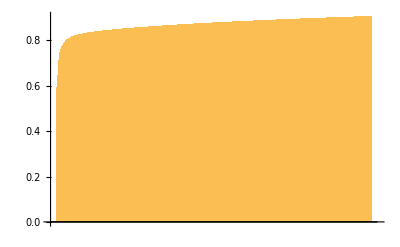

```mathematica
BarChart[totVar[[1;;500]]]
```

```mathematica
Max@Select[totVar,#<0.70&]//Position[totVar,#]&
Max@Select[totVar,#<0.90&]//Position[totVar,#]&
```

{{3}}

{{445}}

#### equivalency to svd

The PrincipalComponents function (“Covariance”) gives the results of SVD on mean zero centered data (unscaled variance). “Correlation” gives SVD on standardized data. 
υ.σ gives PC “scores”; ν is the “loadings”

```mathematica
Xs=Standardize[marrowNorm,Mean,1&]; (* mean centered, variance conserved *)
pos=Position[(var=Variance[marrowNorm]),_?(#>0.&)]//Flatten;
Xss=Quiet@Standardize[marrowNorm[[All,pos]]]; (* mean == 0, std == 1*)
```

```mathematica
{υ,σ,ν}=SingularValueDecomposition[Xs,200];
{υ1,σ1,ν1}=SingularValueDecomposition[Xss,200];
```

```mathematica
T=υ.σ;
TT=υ1.σ1;
T[[1]]//Short
TT[[1]]//Short
```

{132.849,24.5503,1.44496,-3.58032,«192»,-1.27086,1.42701,-0.276657,-0.179219}

{4.33366,-9.41013,-3.73774,0.662551,«192»,1.37685,-1.44198,0.355935,2.11281}

#### KNN graph

```mathematica
marrowGraph=NearestNeighborGraph[P2[[All,1;;50]],15,VertexCoordinates->Automatic,GraphLayout->"SpringElectricalEmbedding"]//IndexGraph;
GraphPlot[marrowGraph]
```

-Graphics-

```mathematica
marrowCoord=GraphEmbedding[marrowGraph,"SpringElectricalEmbedding"];marrowCoord//Short
```

{{19.1964,11.1594},{11.4711,15.083},«5776»,{27.0391,7.5617},{10.7348,8.69163}}

### 3. Laplacian pseudoinverse and kernel PCA

• return the discrete Laplacian/Kirchhoff matrix of the graph, defined as   , where  is the diagonal matrix of  vertex degrees (degree matrix) and  is the adjacency matrix.

```mathematica
L=KirchhoffMatrix[marrowGraph]//N;
(*𝒩=NormalizedLaplacianMat[marrowGraph];*)
```

```mathematica
HermitianMatrixQ/@{L}
```

• this code demonstrates the use of  1/λ	to give eigenvalues equivalent to the pseudoinverse Laplacian eigenvalues

```mathematica
{λm,Um}=-Eigensystem[-L,400,Method->{"Arnoldi",MaxIterations->10^6,Criteria->RealPart}];
```

```mathematica
{λm,Um}=Reverse/@{λm,Um};λm//Short
```

#### a. estimating significant eigenvalues:

```mathematica
Lr=RandomSample[L];
{λr,Ur}=-Eigensystem[-Lr,400,Method->{"Arnoldi",MaxIterations->10^6,Criteria->RealPart}];
{λr,Ur}=Reverse/@{λr,Ur};
```

```mathematica
ListPlot[{1/λm[[2;;60]],Re[1/λr[[2;;60]]+.01]},PlotRange->All]
```

```mathematica
1/λm[[2;;20]]
```

#### b. equivalent results w/pseudo-inverse laplacian

```mathematica
Linv=PseudoInverse[L];
{λ,ϕ}=Eigensystem[Linv,40]//Re;
```

```mathematica
ListPlot[{λ,1/λm[[2;;41]]+0.1},PlotRange->All]
```

```mathematica
Short/@{Um[[2]],ϕ[[1]]}
```

The eigendecomposition of the pseudoinverse Laplacian is used to construct the commute time kernel. First, an embedding is made that preserves commute times/resistance distances, using the inverse square root of the Laplacian eigenvalues (λ). The eigenvalues are ordered in a diagonal matrix (Λ) multiplied by the eigen basis vectors (ϕ). In this notebook, λ is used for the inverse Laplacian values but more generally λ refers to the Laplacian eigenvalues. 

θ = Λ^(1/2)ϕ 	[commute time embedding matrix;  ]   

K_ct= θ^T θ  	[Gram matrix kernel of embedding; commute time kernel] 

K_ct^(1/2)  	[the matrix square root of the commute time kernel is the final kernel form]

```mathematica
Subscript[Θ, 1]=DiagonalMatrix[λ^(1/2)].ϕ;
```

```mathematica
Λ=ϕ.Linv.Transpose[ϕ];
Θ=(Λ^(1/2)).ϕ;
```

```mathematica
Θ.ConstantArray[1,5780]//Chop//Short
```

```mathematica
Kct=Transpose[Θ].Θ;
```

```mathematica
Kct2=MatrixPower[Kct,1/2];
```

### 4. Imputation

• Imputation is applied to the full normalized data matrix.

```mathematica
K2Impute=Kct2.marrowNorm//Re;
```

#### 4a. scaling imputed gene expression

• scale the imputed expression matrix to the 99th percentile of the original normalized data; linearly transform lowest values to zero. 

,

```mathematica
imputeallSc=(Transpose@K2Impute*Map[Quantile[#,0.99]&,Transpose[marrowNorm]])/Map[Max[#,10^-8]&,Transpose[K2Impute]]//Transpose;
```

```mathematica
imputeallSc2=Module[{x},(Transpose[imputeallSc]-Min/@Transpose[imputeallSc])*((Max/@Transpose[imputeallSc])-0)/(x=MinMax[#,10^-8]&/@Transpose[imputeallSc];Differences/@x//Flatten)+0//Transpose];
```

```mathematica
K2Imputed=imputeallSc2;
```

```mathematica
Dimensions[K2Imputed]
```

### 5. Plotting gene expression

```mathematica
Position[marrowGenes,_?(#=="GATA1"&)][[1]][[1]]
```

plotting ‘CD34’, ‘MPO’, ‘GATA1’, ‘IRF8’]) ‘CD34’, ‘MPO’,  ‘CD79B’, ‘ITGA2B’, ‘CSF1R’, ‘GATA1’, ‘CD41’

```mathematica
exp=K2Imputed[[All,Position[marrowGenes,_?(#=="CD34"&)][[1]][[1]]]];
mapPlot=Nearest[marrowCoord[[All,{1,2}]]->Rescale@exp];
colfunArr=cividis@First@mapPlot[{#1,#2}]&;
ListPlot[marrowCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All,PlotLegends->BarLegend[{cividis,{0,1}},LegendLabel->"CD34"]]
```

```mathematica
exp=K2Imputed[[All,Position[marrowGenes,_?(#=="GATA1"&)][[1]][[1]]]];
mapPlot=Nearest[marrowCoord[[All,{1,2}]]->Rescale[exp]];
colfunArr=cividis@First@mapPlot[{#1,#2}]&;
ListPlot[marrowCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All,PlotLegends->BarLegend[{cividis,{0,1}},LegendLabel->"GATA1"]]
```

```mathematica
Export["GATA1.pdf",%]
```

#### 5a. comp to imported force atlas coordinates from tutorial/ magic imputation (OPTIONAL)

```mathematica
tsne=obsm[[All,1]];
magicImputed=obsm[[All,2]];
```

```mathematica
Dimensions@magicImputed
```

```mathematica
exp=marrowNorm[[All,Position[marrowGenes,_?(#=="HBB"&)][[1]][[1]]]];
mapPlot=Nearest[tsne[[All,{1,2}]]->Rescale[exp]];
colfunArr=cividis@First@mapPlot[{#1,#2}]&;
ListPlot[tsne,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

```mathematica
exp=magicImputed[[All,Position[marrowGenes,_?(#=="HBB"&)][[1]][[1]]]];
mapPlot=Nearest[tsne[[All,{1,2}]]->Rescale@exp];
colfunArr=cividis@First@mapPlot[{#1,#2}]&;
ListPlot[tsne,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All,PlotLegends->BarLegend[{cividis,{0,1}},LegendLabel->"HBB"]]
```

#### 5b. gene interaction plots

```mathematica
plk=Position[marrowGenes,_?(#=="PLEK"&)][[1]][[1]];
blv=Position[marrowGenes,_?(#=="BLVRB"&)][[1]][[1]];
itga=Position[marrowGenes,_?(#=="ITGA2B"&)][[1]][[1]];
```

```mathematica
ta1=Transpose[{K2Imputed[[All,plk]],K2Imputed[[All,blv]]}];
ixPlot=Nearest[ta1[[All,{1,2}]]->Rescale[K2Imputed[[All,itga]]]];
colfunArr=cividis@First@ixPlot[{#1,#2}]&;
ListPlot[ta1,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotRange->All,AxesLabel->{"PLEK","BLVRB"},LabelStyle->style1,AspectRatio->1, PlotLegends->BarLegend[{cividis,{0,1}},LegendLabel->"ITGA2B"]]
```

```mathematica
Export["BLVRB.pdf",%]
```

```mathematica
fosl=Position[marrowGenes,_?(#=="FOSL2"&)][[1]][[1]];
irf=Position[marrowGenes,_?(#=="IRF8"&)][[1]][[1]];
mpo=Position[marrowGenes,_?(#=="MPO"&)][[1]][[1]];
```

```mathematica
ta2=Transpose[{K2Imputed[[All,fosl]],K2Imputed[[All,irf]]}];
ixPlot=Nearest[ta2[[All,{1,2}]]->Rescale[K2Imputed[[All,mpo]]]];
colfunArr=cividis@First@ixPlot[{#1,#2}]&;
ListPlot[ta2,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotRange->All,AspectRatio->1,AxesLabel->{"FOSL2","IRF8"},LabelStyle->style1,PlotLegends->BarLegend[{cividis,{0,1}},LegendLabel->"MPO"]]
```

```mathematica
Export["IRF8.pdf",%]
```

```mathematica
spi=Position[marrowGenes,_?(#=="SPI1"&)][[1]][[1]];
gata2=Position[marrowGenes,_?(#=="GATA2"&)][[1]][[1]];
cd34=Position[marrowGenes,_?(#=="CD34"&)][[1]][[1]];
```

```mathematica
ta3=Transpose[{K2Imputed[[All,spi]],K2Imputed[[All,gata2]]}];
ixPlot=Nearest[ta3[[All,{1,2}]]->Rescale[K2Imputed[[All,cd34]]]];
colfunArr=cividis@First@ixPlot[{#1,#2}]&;
ListPlot[ta3,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotRange->All,AspectRatio->1,AxesLabel->{"SPI1","GATA2"},LabelStyle->style1,PlotLegends->BarLegend[{cividis,{0,1}},LegendLabel->"CD34"]]
```

```mathematica
Export["GATA2.pdf",%]
```

### 6. Plotting gene expression on the multiscale k-NN graph

diffusion/commute map embedding and imputation

```mathematica
Dimensions[Θ]
```

```mathematica
Sqrt[5780]//N
```

```mathematica
gr=NearestNeighborGraph[Transpose[Θ],24,VertexCoordinates->Automatic,GraphLayout->"SpringElectricalEmbedding"]//IndexGraph;
```

```mathematica
GraphPlot[gr,EdgeStyle->Thickness[0.0002]]
```

```mathematica
Export["graph.pdf",%]
```

OPTIONAL: sparsify the graph....

```mathematica
span=FindSpanningTree[gr,Method->"Kruskal"];
other=Complement[EdgeList[gr],EdgeList[span]];
gr1=EdgeAdd[span,RandomSample[other,Ceiling[Length[other].5]]]
```

```mathematica
Length[EdgeList[gr]]
Length[EdgeList[gr1]]
```

```mathematica
mapCoord=GraphEmbedding[gr,"SpringElectricalEmbedding"];
```

#### 6a. clusters

```mathematica
clusters=obs[[All,2]];clusters//Short
```

```mathematica
taclust=MapThread[Append,{mapCoord,clusters}];
g=KeySort[GroupBy[taclust,Last,#[[All,{1,2}]]&]];
```

```mathematica
Show[ListPlot[mapCoord,LabelStyle->style1,Axes->False],With[{k=Keys[g]},ListPlot[k/.g,PlotLegends->k,Axes->False,PlotStyle->RGBColor/@clustColors]]]
```

```mathematica
RGBColor["#f781bf"]
```

```mathematica
Export["clusts.pdf",%]
```

explore gene expression
plotting:   ZFP36L2,IRF8,SPI1,HBB,GATA1,ITGA2B,CEBPA,CD79A

ZFP36L2-- HSC marker, Stumpo et al., 2009

```mathematica
GraphPlot[gr,VertexStyle->Thread[VertexList[gr]->cividis/@Rescale[K2Imputed[[All,Position[marrowGenes,_?(#==ToString[GATA1]&)][[1]][[1]]]]]],EdgeShapeFunction->None]
```

```mathematica
Export["ms_gata1.pdf",%]
```

```mathematica
Table[GraphPlot[gr,VertexStyle->Thread[VertexList[gr]->cividis/@Rescale[K2Imputed[[All,Position[marrowGenes,_?(#==ToString[i]&)][[1]][[1]]]]]],EdgeShapeFunction->None],{i,{ZFP36L2,IRF8,SPI1,HBB,GATA1,ITGA2B,CEBPA,CD79A}}]
```

```mathematica
Table[GraphPlot[gr,VertexStyle->Thread[VertexList[gr]->cividis/@Rescale[K2Imputed[[All,Position[marrowGenes,_?(#==ToString[i]&)][[1]][[1]]]]]],EdgeShapeFunction->None],{i,{CD74,ELANE,S100A8,POU2F2,IL7R,CCR7}}]
```

```mathematica
Export["ms_multi2.pdf",%]
```

```mathematica
exp=K2Imputed[[All,Position[marrowGenes,_?(#=="CEBPE"&)][[1]][[1]]]];
mapPlot=Nearest[mapCoord[[All,{1,2}]]->Rescale[exp]];
colfunArr=cividis@First@mapPlot[{#1,#2}]&;
ListPlot[mapCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All,PlotLegends->BarLegend[{cividis,{0,1}},LegendLabel->"IL7R"]]
```

### 7. Pseudotemporal ordering using the commute time kernel

• pseudotime is calculated as an L^1 distance measure using the matrix square root of the commute time kernel to compute the integral of the diffusion map of random walks from cells 
indexed   to :



This commute time pseudotime measure (CtPT) exhibits a higher Pearson correlation to Palantir pseudotime, taken as benchmark, than diffusion pseudotime (dpt), and is roughly similar based on the rank-based linear association Kendall tau.

dpt and root cell from Palantir results:

```mathematica
dpt=Import["data/rep1_dpt.csv"];
dpt=dpt[[2;;,2;;]]//Flatten;
dpt//Short
```

```mathematica
palantir=obs[[All,3]];
palantir//Short
```

```mathematica
Position[palantir,_?(#==0&)]
```

```mathematica
CtPt=Table[Norm[Kct2[[4824]]-Kct2[[j]],1],{j,5780}];
CtPta=Table[Norm[Kct[[4824]]-Kct[[j]],1],{j,5780}];
CtPt2Norm=Table[EuclideanDistance[Kct2[[4824]],Kct2[[j]]],{j,5780}];
```

```mathematica
{KendallTau[CtPt,CtPta],Correlation[CtPt,CtPta]}
```

using mean commute time directly is less informative

```mathematica
commute=Table[Kct2[[i,i]]+Kct2[[j,j]]-2Kct2[[i,j]],{i,{4824}},{j,5780}];
mct=Mean[commute]//Flatten//Re;
```

```mathematica
GraphPlot[marrowGraph,VertexStyle->Thread[VertexList[marrowGraph]->ColorData["Magma"]/@Rescale[mct]],EdgeShapeFunction->None]
```

```mathematica
LPT=Table[Norm[Linv[[4824]]-Linv[[j]],2],{j,5780}];
```

```mathematica
{KendallTau[palantir,dpt],Correlation[palantir,dpt]}
{KendallTau[palantir,CtPt],Correlation[palantir,CtPt]}
{KendallTau[palantir,LPT],Correlation[palantir,LPT]}
```

```mathematica
Table[Correlation[i,j],{i,{LPT,CtPta,CtPt2Norm,CtPt,dpt,palantir}},{j,{LPT,CtPta,CtPt2Norm,CtPt,dpt,palantir}}]//TableForm
```

```mathematica
Table[KendallTau[i,j],{i,{LPT,CtPta,CtPt2Norm,CtPt,dpt,palantir}},{j,{LPT,CtPta,CtPt2Norm,CtPt,dpt,palantir}}]//TableForm
```

```mathematica
Table[KendallTauTest[i,j],{i,{LPT,CtPta,CtPt2Norm,CtPt,dpt,palantir}},{j,{LPT,CtPta,CtPt2Norm,CtPt,dpt,palantir}}]//TableForm
```

```mathematica
GraphPlot[gr,VertexStyle->Thread[VertexList[gr]->ColorData["Magma"]/@Rescale[CtPt]],EdgeShapeFunction->None]
```

```mathematica
Export["palantir.pdf",%]
```

```mathematica
Table[mapPlot=Nearest[mapCoord[[All,{1,2}]]->Rescale[i]];
colfunArr=ColorData["Magma"]@First@mapPlot[{#1,#2}]&;
ListPlot[mapCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All,PlotLegends->BarLegend[{ColorData["Magma"],{0,1}},LegendLayout->"Row"]],{i,{dpt,palantir,CtPt}}]
```

```mathematica
Export["palantir.pdf",%]
```

```mathematica
ta2=Transpose[{Rescale[CtPt],Rescale[palantir]}];
ixPlot=Nearest[ta2[[All,{1,2}]]->Rescale[K2Imputed[[All,cd34]]]];
colfunArr=ColorData["Magma"]@First@ixPlot[{#1,#2}]&;
ListPlot[ta2,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotRange->All,AspectRatio->1,AxesLabel->{"CtPt","Palantir"},LabelStyle->style1,PlotLegends->BarLegend[{ColorData["Magma"],{0,1}},LegendLabel->"CD34"]]
```

```mathematica
Export["cptxpal.pdf",%]
```

```mathematica
EmpiricalDistribution[CtPt]//Kurtosis
```

### 8. Fate probabilities

using manually selected differentiated states from SPRING (Weinreb et al., 2018a).

```mathematica
tips=Import["data/selected_cells(marrow).txt","Data"];
```

```mathematica
tips//Dimensions
```

```mathematica
tips[[1;;10]]
```

add one to correct going form zero-indexing....

```mathematica
tips=(Flatten@tips)+1;tips//Short
```

```mathematica
GraphPlot[gr,GraphHighlight->tips,EdgeShapeFunction->None]
```

```mathematica
subG=Subgraph[gr,tips];subG//GraphPlot
```

```mathematica
clusts=FindGraphCommunities[subG];
cluspos=Select[clusts,(Length[#]>8)&];
```

```mathematica
testAbs=Table[RandomChoice[cluspos[[i]],10],{i,Length[cluspos]}];testAbs//Short
```

```mathematica
Length[testAbs]
```

```mathematica
probs=Table[Table[Kct2.(SparseArray[{i}->1,5780]),{i,testAbs[[j]]}],{j,Length[testAbs]}]//Re;
```

```mathematica
probs[[1]]//Short
```

```mathematica
Mean@probs[[1]]//Dimensions
```

```mathematica
mapPlot=Nearest[mapCoord[[All,{1,2}]]->Rescale[Mean@probs[[4]]]];
colfunArr=ColorData["Magma"]@First@mapPlot[{#1,#2}]&;
ListPlot[mapCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

Use states to match those used w/Palantir in Setty et al.  (2019):

```mathematica
tabP=Table[Mean[probs[[i]]],{i,{8,3,5,7,6,4}}];
```

```mathematica
mapPlot=Nearest[mapCoord[[All,{1,2}]]->Rescale[tabP[[1]]]];
colfunArr=ColorData["Magma"]@First@mapPlot[{#1,#2}]&;
ListPlot[mapCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

terminal states : 1 = lymphocyte; 2 = Erythrocyte; 3 = Monocyte; 4 = Neutrophil; 5 = Mega; 6 = pDC; 7 = cDC; ;

```mathematica
Dimensions/@{probs,tabP}
```

transpose for prob per lineage

```mathematica
tabPᵀ[[70]]//Normalize
```

Run5_164698952452459

```mathematica
cell1=Position[obs,_?(#=="Run5_131097901611291"&)][[1]][[1]];
cell2=Position[obs,_?(#=="Run5_134936662236454"&)][[1]][[1]];
cell3=Position[obs,_?(#=="Run4_200562869397916"&)][[1]][[1]];
cell4=Position[obs,_?(#=="Run5_164698952452459"&)][[1]][[1]];
```

```mathematica
{BarChart[tabPᵀ[[cell1]]//Normalize],BarChart[tabPᵀ[[cell2]]//Normalize],BarChart[tabPᵀ[[cell3]]//Normalize],BarChart[tabPᵀ[[cell4]]//Normalize]}
```

```mathematica
Export["lin_probs.pdf",%]
```

```mathematica
ResourceData["GraphHighlightStyle"]
```

```mathematica
(*GraphPlot[gr,GraphHighlight->{cell1,cell2,cell3,cell4},GraphHighlightStyle->"DehighlightFade",EdgeShapeFunction->None] *)
(*HighlightGraph[gr,{cell1,cell2,cell3,cell4},VertexSize->.2,EdgeShapeFunction->None]*)
Show[GraphPlot[gr,EdgeShapeFunction->None],HighlightGraph[gr,{cell1,cell2,cell3,cell4},VertexStyle->Red,VertexSize->100,GraphHighlightStyle->"DehighlightHide",EdgeShapeFunction->None]]
```

```mathematica
Table[mapPlot=Nearest[mapCoord[[All,{1,2}]]->Rescale[Mean@probs[[i]]]];
colfunArr=ColorData["WL12DefaultVectorGradient"]@First@mapPlot[{#1,#2}]&;
ListPlot[mapCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All(*,PlotLegends->BarLegend[{ColorData["TemperatureMap"],{0,1}}]*)],{i,{8,3,5,7,6,4}}]
```

```mathematica
Export["prob_array.pdf",%]
```

terminal states : 1 = lymphocyte; 2 = Erythrocyte; 3 = Monocyte; 4 = Neutrophil; 5 = Mega; 6 - pDC; 7 =cDC; ;

Get previously computed branch probabilities:  /uns/palantir_branch_probs_cell_types

```mathematica
palProbs=obsm[[All,3]];
```

```mathematica
Import[h5adFile,{"Datasets","/uns/palantir_branch_probs_cell_types"}]
```

```mathematica
Table[mapPlot=Nearest[mapCoord[[All,{1,2}]]->Rescale[palProbs[[All,i]]]];
colfunArr=ColorData["WL12DefaultVectorGradient"]@First@mapPlot[{#1,#2}]&;
ListPlot[mapCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All,PlotLegends->BarLegend[{ColorData["WL12DefaultVectorGradient"],{0,1}}]],{i,6}]
```

terminal states : 1 = Neutrophil; 2 = Erythrocyte; 3 = pDC; 4 = Mega; 5 = CLP/Lympho; 6  = cDC;

```mathematica
Export["prob_palan.pdf",%]
```

```mathematica
Table[KendallTau[Mean@probs[[i]],palProbs[[All,j]]],{i,{8,3,5,7,6,4}},{j,{1,2,3,4,5,6}}]//Diagonal
```

```mathematica
Table[Correlation[Mean@probs[[i]],palProbs[[All,j]]],{i,{8,3,5,7,6,4}},{j,{1,2,3,4,5,6}}]//Diagonal
```

```mathematica
Table[KendallTauTest[Mean@probs[[i]],palProbs[[All,j]]],{i,{8,3,5,7,6,4}},{j,{1,2,3,4,5,6}}]//Diagonal
```

#### alt tip method...

```mathematica
ecc=VertexEccentricity[gr,#]&/@VertexList[gr];
ecc=Flatten[Ordering[ecc,-650]];
```

```mathematica
GraphPlot[gr,GraphHighlight->cenOrd,EdgeShapeFunction->None]
```

```mathematica
cen=1/Diagonal[Linv];
cenOrd=Ordering[Normal@cen,750];
```

```mathematica
subG2=Subgraph[gr,cenOrd];subG2//GraphPlot
```

```mathematica
cen[[root]]
```

```mathematica
Min[cen]
```

```mathematica
Position[cen,_?(#==Min[cen]&)]
```

### 9. Trajectory analysis -- finding gene expression trends

terminal states : 1 = lymphocyte; 2 = Erythrocyte (GATA1); 3 = Monocyte; 4 = Neutrophil; 5 = Mega; 6 = pDC; 7 = cDC (SPI1);  from above   (3&4 v 2&6)
{Mono,Ery,pDC,Mega,CLP,cDC}

```mathematica
mapPlot=Nearest[mapCoord[[All,{1,2}]]->Rescale[tabP[[6]]]];
colfunArr=ColorData["Magma"]@First@mapPlot[{#1,#2}]&;
ListPlot[mapCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

```mathematica
psta1=Transpose[{Rescale[CtPt],Rescale[K2Imputed[[All,Position[marrowGenes,_?(#=="SPI1"&)][[1]][[1]]]]]}];
mapPlot=Nearest[psta1[[All,{1,2}]]->Rescale[tabP[[6]]]];
colfunArr=ColorData["Magma"]@First@mapPlot[{#1,#2}]&;
ListPlot[psta1,PlotLegends->{"GATA1"},PlotRange->All,ColorFunction->colfunArr,ColorFunctionScaling->False,PlotStyle->PointSize[Medium]]
```

```mathematica
model=a x+b x^2+c x^3+d x^4;
```

```mathematica
(*glm=GeneralizedLinearModelFit[psta1,x,x,ExponentialFamily->"Gamma",Weights->Rescale[Mean@probs[[6]]]]*)
```

```mathematica
nlm=NonlinearModelFit[psta1,model,{a,b,c,d},x,Weights->Rescale[tabP[[6]]]]
```

```mathematica
nlm["MeanPredictionBands",ConfidenceLevel->.5]
```

```mathematica
bands90[x_]=nlm["MeanPredictionBands",ConfidenceLevel->.95];
Show[ListPlot[psta1],Plot[{nlm[x],bands90[x]},{x,0,1},Filling->{2->{1}}],PlotRange->{{0,1},{0,1}}]
```

Palantir w/ MAGIC (import magic if not done previously)

```mathematica
magicImputed=obsm[[All,2]];
Dimensions[magicImputed]
```

```mathematica
psta2=Transpose[{Rescale[palantir],Rescale[magicImputed[[All,Position[marrowGenes,_?(#=="SPI1"&)][[1]][[1]]]]]}];
mapPlot=Nearest[psta2[[All,{1,2}]]->Rescale[palProbs[[All,6]]]];
colfunArr=ColorData["Magma"]@First@mapPlot[{#1,#2}]&;
ListPlot[psta2,PlotLegends->{"SPI1"},PlotRange->All,ColorFunction->colfunArr,ColorFunctionScaling->False,PlotStyle->PointSize[Medium]]
```

```mathematica
model=a x+b x^2+c x^3+d x^4;
```

```mathematica
nlm2=NonlinearModelFit[psta2,model,{a,b,c,d},x,Weights->Rescale[palProbs[[All,6]]]]
```

```mathematica
bands90a[x_]=nlm2["MeanPredictionBands",ConfidenceLevel->.95];
Show[ListPlot[psta2],Plot[{nlm2[x],bands90a[x]},{x,0,1},Filling->{2->{1}}],PlotRange->{{0,1},{0,1}}]
```

```mathematica
Show[Plot[{nlm[x],bands90[x]},{x,0,1},Filling->{2->{1}},PlotLabels->{"Kct"}],Plot[{nlm2[x],bands90a[x]},{x,0,1},Filling->{2->{1}},PlotStyle->Dashed,PlotLabels->{"Palantir"}],PlotRange->{{0,1},{0,1}},LabelStyle->style1,AxesLabel->{"pseudotime","SPI1"}]
```

```mathematica
Export["spi_trend.pdf",%]
```

### 9a. gene expression trends 2

```mathematica
psta3=Transpose[{Rescale[CtPt],Rescale[K2Imputed[[All,Position[marrowGenes,_?(#=="GATA1"&)][[1]][[1]]]]]}];
psta4=Transpose[{Rescale[CtPt],Rescale[K2Imputed[[All,Position[marrowGenes,_?(#=="SPI1"&)][[1]][[1]]]]]}];
```

```mathematica
(*Dxy=SmoothKernelDistribution[psta2,{"Standardized",1/2},"Gaussian"];*)
Dxy=SmoothKernelDistribution[psta4,0.05,"Gaussian"];
Dx=SmoothKernelDistribution[Rescale[CtPt],0.05,"Gaussian"];
Dy=SmoothKernelDistribution[Rescale[K2Imputed[[All,Position[marrowGenes,_?(#=="SPI1"&)][[1]][[1]]]]],0.05,"Gaussian"];
DensityPlot[PDF[Dxy,{xx,yy}],{xx,0,1},{yy,0,1},PlotRange->All]
```

```mathematica
cond=PDF[Dxy,{xx,yy}]/Max[PDF[Dy,yy],10^-8];
```

```mathematica
DensityPlot[cond,{xx,0,Max[psta4[[All,1]]]},{yy,0,Max[psta4[[All,2]]]},PlotRange->All,Frame->False]
```

### 10. export to SPRING:

```mathematica
CreateDirectory["marrow"];
```

#### # color_data_all_genes

```mathematica
II=Round[Length[marrowGenes]/50]+1
```

```mathematica
Z=Insert[marrowNorm,marrowGenes,1]ᵀ;Z//Dimensions
```

```mathematica
pos=Position[Mean/@Z[[All,2;;]],_?(#>0.05&)]
```

```mathematica
Quantile[Mean/@Z[[All,2;;]],0.5]
```

```mathematica
ZZ=Extract[Z,pos];ZZ//Dimensions
```

```mathematica
parts=Partition[ZZ,II];parts//Dimensions
```

```mathematica
Module[{fname,customColors},Do[
fname="marrow/gene_colors/color_data_all_genes-"<>ToString[j-1]<>".csv";
customColors=parts[[j]];
Export[fname,customColors,"CSV","TextDelimiters"->""],{j,Length[parts]}]]
```

#### # color stats

```mathematica
colorStats=Module[{mean,std,min,max,centile,colorStats},colorStats=List[];
Do[mean=Mean[marrowNorm[[All,i]]];
std=StandardDeviation[marrowNorm[[All,i]]];
min=Min[marrowNorm[[All,i]]];max=Max[marrowNorm[[All,i]]];centile=Quantile[marrowNorm[[All,i]],0.996];
AppendTo[colorStats,{mean,std,min,max,centile}];,{i,Length[marrowGenes]}];colorStats];
colorStats//Short
```

```mathematica
testThread=Table[Thread[marrowGenes[[i]]->colorStats[[i]],List,1],{i,Length[marrowGenes]}];
testThread//Short
```

```mathematica
Export["marrow/color_stats.json",testThread, "JSON","Compact"->False]
```

#### # write graph

{  “nodes”: [ {   “name”: cell0, “number”: 0 },     // List of nodes
                   {   “name”: cell1, “number”: 1 },
                   ....
                   {   “name”: cellN, “number”: N } ],
        “links”: [ { “source”: 10, “target”: 23 },      // List of edges
                   { “source”: 29, “target”: 50 },
                   ....
                   { “source”: 40, “target”: 125 }  ] }

```mathematica
names=VertexList[gr];
numbers=VertexList[gr]; (*let's try degree-based colouring*)

Export["marrow/graph_data.json",{"nodes"->MapThread[{"name"->#1-1,"number"->#2-1}&,{names,numbers}],"links"->({"source"->#1-1,"target"->#2-1,"distance"->0}&)@@@EdgeList[gr]},"JSON"]
```

#### # save custom colors

custom_colors[‘Uniform’] = np.zeros(E.shape[0])
    write_color_tracks(custom_colors, project_directory+‘color_data_gene_sets.csv’)
    
    use {} to ensure commas

```mathematica
pseudotime=CtPt;
```

```mathematica
customColors1=ConstantArray[0,Dimensions[marrowNorm][[1]]]//Prepend[#,"Uniform"]&;
customColors2=pseudotime//Prepend[#,"pseudotime"]&;
customColorSet=Join[{customColors1},{customColors2}];
```

```mathematica
customColorSet[[2]]//Short
```

```mathematica
Export["marrow/color_data_gene_sets.csv",{customColors2},"CSV","TextDelimiters"->""]
```

#### # coordinates

```mathematica
newmap=Transpose[Insert[Transpose[mapCoord*100],Range[0,Length[mapCoord]-1],1]];
```

```mathematica
Export["marrow/coordinates.txt",Flatten/@newmap,"CSV"]
```

#### # total counts, gene list, (opt)

```mathematica
totCounts=Total[marrowData,{2}];
totCounts//Short
```

```mathematica
Export["total_counts.txt",totCounts]
```

```mathematica
Export["genes.txt",marrowGenes]
```

a = {{1, 2, 3}, {4, 0, 8}, {7 , 8, 0}}
column = {97, 98, 99}
newa = Transpose[Insert[Transpose[a], column, 2]]

```mathematica
Export["cell_filter.txt",Range[Length[geneList]]-1]
```

#### # color tracks (old)

write_color _tracks (custom_colors, strcat (project_directory, ' color_data _gene _sets . csv'));

```mathematica
dims=Dimensions[marrowNorm]+1
```

```mathematica
II=Round[Length[marrowGenes]/50]+1;
geneList=Partition[marrowGenes,II];
normList=Partition[marrowNormᵀ,II];
```

```mathematica
Length[geneList]
```

```mathematica
Module[{fname},Do[
fname="gene_colors/color_data_all_genes-"<>ToString[j-1]<>".csv";
AllGeneColors=Insert[normList[[j]]ᵀ,geneList[[j]],1]ᵀ;
Export[fname,AllGeneColors],{j,Length[geneList]}]]
```

```mathematica
Close["/Users/houon/gene_colors/color_data_all_genes-0.csv"]
```

#### # edges (opt)

```mathematica
edges=EdgeList[gr];edges//Short
```

```mathematica
edges=List@@@edges;
```

```mathematica
Export["edges.csv",edges]
```

#### # Hdf5 files (test)

In[15]:= Import[“file.h5”, {“DataEncoding”, “/input_image”}]

```mathematica
test=Import["/Users/houon/Documents/counts_norm_sparse_genes.hdf5",{"DataEncoding","/counts/"}]
```

```mathematica
test2=Import["/Users/houon/Documents/counts_norm_sparse_cells.hdf5","/counts"]
```

Export[“m1.h5”, “/m1” -> {
   “Data” -> Range[5], 
   “DataFormat” -> “UnsignedInteger8”
   }]

```mathematica
counts=Table[marrowNorm[[i,All]],{i,Dimensions[marrowNorm][[1]]}];
Export["counts_norm_sparse_genes.hdf5","/counts"->marrowNorm,"/gene_ix"->marrowGenes]
```

### 11. References

Setty, M., Kiseliovas, V., Levine, J., Gayoso, A., Mazutis, L., Pe’er, D., 2019. Characterization of cell fate probabilities in single-cell data with Palantir. Nat Biotechnol 37, 451–460. https://doi.org/10.1038/s41587-019-0068-4

Stumpo, D.J., Broxmeyer, H.E., Ward, T., Cooper, S., Hangoc, G., Chung, Y.J., Shelley, W.C., Richfield, E.K., Ray, M.K., Yoder, M.C., Aplan, P.D., Blackshear, P.J., 2009. Targeted disruption of Zfp36l2, encoding a CCCH tandem zinc finger RNA-binding protein, results in defective hematopoiesis. Blood 114, 2401–2410. https://doi.org/10.1182/blood-2009-04-214619

van Dijk, D., Sharma, R., Nainys, J., Yim, K., Kathail, P., Carr, A.J., Burdziak, C., Moon, K.R., Chaffer, C.L., Pattabiraman, D., Bierie, B., Mazutis, L., Wolf, G., Krishnaswamy, S., Pe’er, D., 2018. Recovering Gene Interactions from Single-Cell Data Using Data Diffusion. Cell 174, 716-729.e27. https://doi.org/10.1016/j.cell.2018.05.061

Weinreb, C., Wolock, S., Tusi, B.K., Socolovsky, M., Klein, A.M., 2018. Fundamental limits on dynamic inference from single-cell snapshots. Proceedings of the National Academy of Sciences 115, E2467–E2476. https://doi.org/10.1073/pnas.1714723115

Weinreb, C., Wolock, S., Klein, A.M., 2018a. SPRING: a kinetic interface for visualizing high dimensional single-cell expression data. Bioinformatics 34, 1246–1248. https://doi.org/10.1093/bioinformatics/btx792